```mathematica
(* This notebook aims to test the scaling law of infidility and trace distance measure 
for randomly generated bath states and interaction Hamiltonians *)
```

```mathematica
TrB[A_]:=Map[Tr,Partition[A,{2,2}],{2}]
TrS[A_]:=A[[1;;2,1;;2]]+A[[3;;4,3;;4]]
BathPart[Ω_]:=0.5TrS[Ω];
SBPart[Ω_]:=Ω-0.5KroneckerProduct[Id,TrS[Ω]];
ErrorPhase[Ω_]:=Norm[SBPart[Ω]]
BathPhase[Ω_]:=Norm[BathPart[Ω]]
TrNorm[A_]:=Total[SingularValueList[A]]
TrDist[ρ_,σ_]:=1/2 TrNorm[ρ-σ];
Fidelity[ρ_,σ_]:=TrNorm[MatrixPower[ρ,1/2].MatrixPower[σ,1/2]];
InFid[ρ_,σ_]:=1-Fidelity[ρ,σ];
Overlap[ρ_,σ_]:=Re[Tr[ρ.σ]];
Purity[ρ_]:=Tr[ρ.ρ]; 
FNorm[A_]:=Norm[A,"Frobenius"];
KetBra[x_,y_]:=KroneckerProduct[Conjugate[x],y];
Pure2Dens[x_]:=KetBra[x,x];
Dens2Bloc[A_]:=Table[Tr[A.PauliMatrix[i]],{i,0,3}];
Bloc2Dens[A_]:=1/2Sum[A⟦i+1⟧*PauliMatrix[i],{i,0,3}]; 
OverlapBloc[x_,y_]:=1/2x.y;
TrDistBloc[x_,y_]:=1/2Norm[x-y];
{Id,X,Y,Z}={σ[0],σ[1],σ[2],σ[3]}=Table[PauliMatrix[i],{i,0,3}];
(* Generating random Hamiltonian operators with (α,β) *)
RandomOmega[α_,β_]:=Module[{HS,HSB},
HS=KroneckerProduct[σ[0],RandomReal[{-1,1},3].Array[σ,3]];
HSB=Sum[KroneckerProduct[σ[i],RandomReal[{-1,1},4].Array[σ,4,0]],{i,1,3}];
α HS/Norm[HS]+β HSB/Norm[HSB]
]
(* The final system state according to the open system dynamics *)
SysEvolve[U_,ρ0_]:=TrB[U.ρ0.U†]
(* Convert the channel to PTM *)
GenPTM[U_,ρB_]:=Table[
Chop[1/2Tr[σ[i].SysEvolve[U,KroneckerProduct[σ[j],ρB]]]],{i,0,3},{j,0,3}]
```

```mathematica
(* Comparing different figure of merit *)
ρS={{1,0},{0,0}};
ρB={{1,0},{0,0}};
ρ0=KroneckerProduct[ρS,ρE];
Ω=RandomOmega[0.1,0.1];
ρSt=SysEvolve[MatrixExp[-ⅈ Ω],ρ0];
{r,s}=Dens2Bloc/@{ρS,ρSt};
{Overlap[ρS,ρSt],OverlapBloc[r,s],√Overlap[ρS,ρSt],Fidelity[ρS,ρSt],TrDist[ρS,ρSt],TrDistBloc[r,s]}
```

{0.998932,0.998932+0. ⅈ,0.999466,0.999466,0.00627401,0.00627401}

```mathematica
GenPTM[U,ρB]//MatrixForm
```

(1. | 0 | 0 | 0
0.00281249 | 0.993541 | 0.00190257 | 0.073641
0.000780515 | -0.0038426 | 0.99633 | 0.0275194
0.00117153 | -0.0757448 | -0.0291756 | 0.995437)

```mathematica
(* Measure 1: Infidelity Maximized over all system states *)
```

```mathematica
MaxInfid[U_,ρB_]:=Module[{M,x,y,z,s},
M=GenPTM[U,ρB];
s=NMinimize[{1,x,y,z}.M.{1,x,y,z},{x,y,z}∈Sphere[]][[1]];
1-√(s/2)]
```

```mathematica
(* Measure 2: Trace distance maximized over all system states *)
MaxTrDist[U_,ρB_]:=Module[{M,x,y,z,s},
M=GenPTM[U,ρB];
0.5*NMaximize[Norm[{1,x,y,z}-M.{1,x,y,z}],{x,y,z}∈Sphere[]][[1]]
]
```

```mathematica
(* Verifying Trace Distance inequality *)
Module[{td,inf},
td=MaxTrDist[U,ρB];
inf=MaxInfid[U,ρB];
{inf,td,√(inf(2-inf))}]
```

{0.0010557,0.0401202,0.0459378}

```mathematica
(* Maximal infidelity vs β, with fixed α=0.1 *)
```

```mathematica
InFidvsBeta=ParallelTable[{β,MaxInfid[RandomOmega[0.1,β],ρB]},{β,0,0.2,0.01}];
```

```mathematica
Exp[b]/.FindFit[Log[Rest[InFidvsBeta]],2x+b,b,x]
```

0.32205

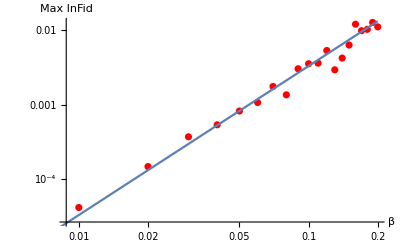

```mathematica
Show[ListLogLogPlot[Rest[InFidvsBeta],PlotStyle->Red,AxesLabel->{"β","Max InFid"}],LogLogPlot[1/3 x^2,{x,0,0.2}]]
```

```mathematica
TrDistvsBeta=ParallelTable[{β,MaxTrDist[RandomOmega[0.1,β],ρB]},{β,0,0.2,0.01}];
```

```mathematica
Exp[b]/.FindFit[Log[Rest[TrDistvsBeta]], x+b,{b},x]
```

0.426743

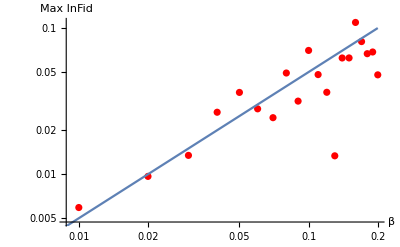

```mathematica
Show[ListLogLogPlot[Rest[TrDistvsBeta],PlotStyle->Red,AxesLabel->{"β","Max InFid"}],LogLogPlot[0.5 x,{x,0,0.2}]]
```

```mathematica
(* Testing a lot of points for more confidence *)
```

```mathematica
InFidvsBeta2=ParallelTable[
{β=RandomReal[{0,0.2}],MaxInfid[RandomOmega[0.1,β],ρB]},200];
```

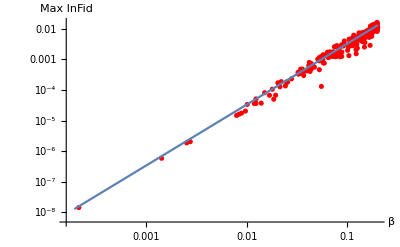

```mathematica
Show[ListLogLogPlot[Rest[InFidvsBeta2],PlotStyle->Red,AxesLabel->{"β","Max InFid"}],LogLogPlot[1/3 x^2,{x,0,0.2}]]
```

```mathematica
TrDistvsBeta2=ParallelTable[
{β=RandomReal[{0,0.2}],MaxTrDist[RandomOmega[0.1,β],ρB]},200];
```

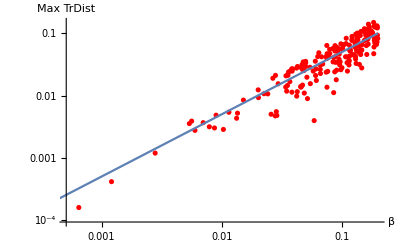

```mathematica
Show[ListLogLogPlot[Rest[TrDistvsBeta2],PlotStyle->Red,AxesLabel->{"β","Max TrDist"}],LogLogPlot[0.5 x,{x,0,0.2}]]
```

```mathematica
Fidvsα=Table[{α,Module[{β=0.1},
Ht=α KroneckerProduct[Id,B0]+β (KroneckerProduct[X,B1]+KroneckerProduct[Y,B2]+KroneckerProduct[Z,B3]);
U0=MatrixExp[-ⅈ Ht];
rhoT=U0.rho0.U0†;
rhoST=Map[Tr,Partition[rhoT,{2,2}],{2}];
(1-Tr[rhoS.rhoST])//Chop]},{α,0.0,0.2,0.01}]
```

{{0.,0.00990559},{0.01,0.00990569},{0.02,0.00990577},{0.03,0.00990582},{0.04,0.00990584},{0.05,0.00990583},{0.06,0.0099058},{0.07,0.00990573},{0.08,0.00990564},{0.09,0.00990552},{0.1,0.00990538},{0.11,0.0099052},{0.12,0.009905},{0.13,0.00990477},{0.14,0.00990451},{0.15,0.00990422},{0.16,0.0099039},{0.17,0.00990356},{0.18,0.00990319},{0.19,0.00990279},{0.2,0.00990236}}

```mathematica
FidvsαPDD=Table[{α,Module[{β=0.1},
Ht=α KroneckerProduct[Id,B0]+β (KroneckerProduct[X,B1]+KroneckerProduct[Y,B2]+KroneckerProduct[Z,B3]);
U0=MatrixExp[-ⅈ Ht];
UDD=KroneckerProduct[Z,Id].U0.KroneckerProduct[X,Id].U0.KroneckerProduct[Z,Id].U0.KroneckerProduct[X,Id].U0;
rhoT=UDD.rho0.UDD†;
rhoST=Map[Tr,Partition[rhoT,{2,2}],{2}];
(1-Tr[rhoS.rhoST])//Chop]},{α,0.0,0.2,0.01}]
```

{{0.,0.000700777},{0.01,0.000707755},{0.02,0.000717969},{0.03,0.00073141},{0.04,0.000748069},{0.05,0.000767933},{0.06,0.000790987},{0.07,0.000817213},{0.08,0.00084659},{0.09,0.000879094},{0.1,0.000914699},{0.11,0.000953377},{0.12,0.000995095},{0.13,0.00103982},{0.14,0.00108751},{0.15,0.00113814},{0.16,0.00119165},{0.17,0.00124801},{0.18,0.00130717},{0.19,0.00136908},{0.2,0.00143368}}

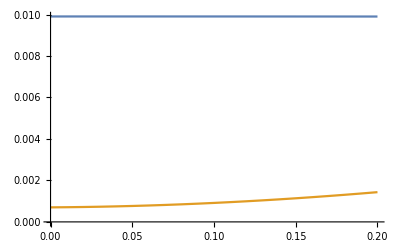

```mathematica
ListPlot[{Fidvsα,FidvsαPDD},Joined->True]
```

```mathematica
A=Normalize[RandomReal[{0,1},3].Array[σ,3],FNorm]
```

{{0.274682+0. ⅈ,0.205524-0.618312 ⅈ},{0.205524+0.618312 ⅈ,-0.274682+0. ⅈ}}

```mathematica
{FNorm[A],Norm[A]}
```

{1.41421,1.}

```mathematica
{FNorm[KroneckerProduct[A,IdentityMatrix[2]]],Norm[KroneckerProduct[A,IdentityMatrix[2]]]}
```

{1.41421,0.707107}

```mathematica
A=Normalize[RandomReal[{0,1},3].Array[σ,3],Norm]
```

{{0.814937+0. ⅈ,0.328676-0.477337 ⅈ},{0.328676+0.477337 ⅈ,-0.814937+0. ⅈ}}

```mathematica
Norm[A]
```

1.

```mathematica
Normalize[RandomReal[{0,1},3].Array[σ,3],FNorm]
```

```mathematica
A=Sum[KroneckerProduct[σ[i],(RandomReal[{0,1},4].Array[σ,4,0])],{i,1,3}];A//MatrixForm
```

(0.983574+0. ⅈ | 0.527727-0.959117 ⅈ | 1.48127-0.837794 ⅈ | -0.708547-1.10653 ⅈ
0.527727+0.959117 ⅈ | -0.903973+0. ⅈ | 1.01289-0.480978 ⅈ | 0.134415+0.13401 ⅈ
1.48127+0.837794 ⅈ | 1.01289+0.480978 ⅈ | -0.983574+0. ⅈ | -0.527727+0.959117 ⅈ
-0.708547+1.10653 ⅈ | 0.134415-0.13401 ⅈ | -0.527727-0.959117 ⅈ | 0.903973+0. ⅈ)

```mathematica
Norm[A]
```

2.89137

{{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}